# ЛР1. Актуализация знаний 1-ого семестра.

## 1. Работаем со списками и элементарными вычислениями.

### 1.1

Докажите эмпирически (с помощью вычислений) сходимость числового ряда ∑_(n=0)^∞ (-1)^n/(2n+1).  Сделайте предположение о том, к какому числу сходится ряд. Подтвердите вычисления графически.

### 1.2

Докажите эмпирически расходимость  ряда. ∑_(n=1)^∞ 1/n. Для этого можно доказать, что для любого числа K, существует N, такое что ∑_(n=1)^N 1/n> K.

### Пример

```mathematica
1/(#!)&/@Range[0,30](*Первый 31 член ряда*)
```

```mathematica
1/(#!)&/@Range[0,30]//Total//N[#,30]&(*Частичная сумма первых 31 члена*)
```

```mathematica
ⅇ-(1/(#!)&/@Range[0,30]//Total//N[#,30]&)(*Предполагаем, что ряд сходится к экпоненте*)
```

```mathematica
Table[Abs[ⅇ-(1/(#!)&/@Range[0,i]//Total)],{i,1,30}]//N[#,50]&(*смотрим, как погрешность изменяется с увеличением количества членов ряда*)
```

## 2. Пишем собственные функции.

### Вычисление числа π методом Монте-Карло. Теория.

Идея метода в случайном распределении точек. Зададим некторое количество случайных точек в квадрате 0 ≤ x ≤ 1, 0 ≤ y ≤ 1.

```mathematica
Short[pts=RandomReal[{0,1},{1000,2}]]
```

Очевидно, что геометрически точки будут лежать внутри квадарата со строной 1. Если вписать в этот квадрат окружность, то логично, что часть точек окажется в ней.

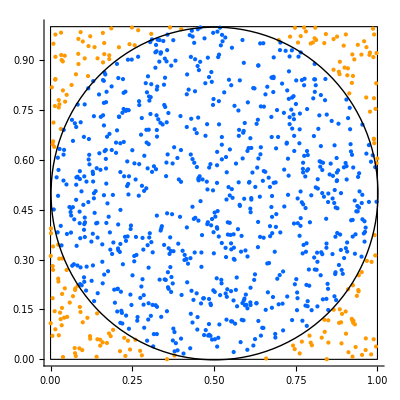

Далее логично предположить, что отношение площадей фигур будет “равно” или, лучше сказать, “близко”, отношению количества точек внутри каждой фигуры. 
Тогда если K - это количество точек в круге, а N - общее количество точек  (лежащих в квадрате), то K/N=S_круга/S_квадарата. 
Площади круга и квадарта мы можем вычислить. S_круга=π*1/4, S_квадрата=1.  
Получаем финальное соотношение, откуда выражаем π. π = 4 * K/N.

Остаётся только найти количечество точек внутри окуржности исходя из геометрических свойств. С увеличением количества точек, ожидаем увеличение точности.

### 2.1

Реализуйте функцию для вычисления числа π методом Монте-Карло. На вход функция принимает, количество точек. Исследуйте, как меняется точность вычислений с увеличением количества точек.

## 3. Вспоминаем графические примитивы.

Модифицируйте функцию из задания 2.1 таким образом, чтобы она также возвращала графическую визуализацию работы метода.

## 4. Динамические вычисления.

### 4.1.

Реалиузйте функцию принмиающую на вход полином и возвращающую все его корни, а также графическую интерпретацию эдействительных корней.

### Пример.

Пусть задано уравнение.

```mathematica
eqn = x^7+7 x^3+x^2+11==0
```

```mathematica
eqn//Solve//Values//N//Flatten(*получили корни*)
```

```mathematica
rootsreal=eqn//Solve//Values//N//Flatten//Cases[#,_Real]&(*вот так можно получить дествительные корни*)
```

Для получение визуализации лучше использовать функцию Plot с опцией Epilog.

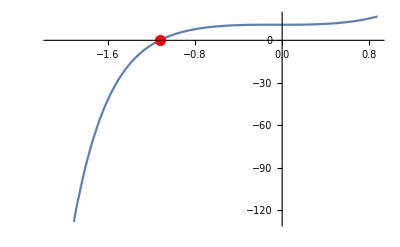

### 4.2

Реализуйте с помщью функции Manipulate скрипт аналогичный предыдущему. Теперь один из коэффициентов полинома - параметр. Продемонстируйте изменения графической интерпретации при изменении параметра.

```mathematica
x^7+7 x^3+a*x^2+11==0
```

### 4.3

Реалиузйте функцию принмиающую на вход полином и возвращающую все его корни, а также графическую интерпретацию комплексных корней. Комплексные корни стоит отрисовать на комплексной плоскости.  Подпишите их.

```mathematica
rootscomplex=eqn//Solve//Values//N//Flatten//Cases[#,_Complex]&
```